# Mathematica Prof. Spaletta & Prof. Ritelli

## Ivo Bonfanti 0001178865

## Exercise 7

Evaluate the integral,
											  T=∫_0^∞ (x ln(x))/(1+x^3)ⅆx

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define the integrand function*)
f[x_] := x Log[x]/(1+x^3)
```

```mathematica
(*Define the original integral*)
T:=Integrate[f[x],{x,0,Infinity}]
```

The integral cannot be solved through algebraic manipulations nor by integration by parts, since the integrand lacks an elementary antiderivative. An alternative approach involves leveraging special functions within the complex domain.

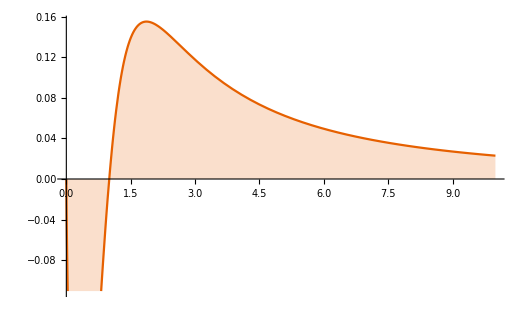

```mathematica
(*Plot the integrand function*)
Plot[f[x], {x, 0, 10}, Filling->Axis]
```

### The Beta function

The Beta function can be expressed in several ways. Among the different representations the following is the one most similarly structured to integral T:

								     		   B(c, d)=∫_0^∞ s^(c-1)/(1+s)^(c+d)ⅆs.

```mathematica
(*Plot the Beta function*)
Plot3D[Beta[x,y],{x,0,5},{y,0,5},AxesLabel->{"x","y","Beta(x, y)"},PlotLabel->"3D Plot of Beta(x, y)"]
```

-Graphics3D-

### Relationship with the Beta function

Now, consider the function:
											   j(a)=∫_0^∞ x^a/(1+x^3)ⅆx.

```mathematica
(*Define the integrand function*)
g[x_,a_]:= x^a/(1 + x^3)
```

```mathematica
(*Define the integral function*)
j[a_]:=Integrate[g[x,a],{x,0,Infinity}]
```

It is easy to show that the first derivative of the latter function, evaluated in a_0=1, is equal to the original integral T. Indeed, following a special case of the Leibniz integral rule (1):

							 ∂_a j(a)=∫_0^∞ ∂_a (x^a/(1+x^3))ⅆx.

However the rule can be applied under certain conditions (2):
a) The integrand f(x,a) and its partial derivative ∂_a f(x,a) are continuous functions when x is in the range of integration and a is in some interval around a_0.

```mathematica
(*Find the domain of the integrand*)
FunctionDomain[g[x,a], {x,a}]
```

(a∈ℤ&&x≠-1&&x≠0)||(a∈ℤ&&x≠-1&&a≥1)||(x≥0&&a>0)||x>0

```mathematica
(*Derive the integrand*)
gprime=D[g[x,a], a]
```

(x^a Log[x])/(1+x^3)

```mathematica
(*Find the domain of the partial derivative of the integrand*)
FunctionDomain[gprime, {x,a}]
```

x>0

The integrand f(x,a) and its partial derivative ∂_a f(x,a) are continuous for x≠−1 and for x≠0. Since x=0 belongs to the range of integration this condition is not fully met.

b) For a in some interval around a_0 there are upper bounds |f(x, a)|≤A(x) and |∂_a f(x, a)|≤B(x), both bounds being independent of a, such that ∫_b^c A(x)ⅆx and ∫_b^c B(x)ⅆx exist.

Let’s first check the convergence of ∫_0^∞ |f(x, a)| ⅆx. 
For x→0:

```mathematica
(*Expand the integrand near x=0 and select the leading term, the one with the smallest exponent since x->0*)
series=Series[g[x,a],{x,0,1}]//Normal
```

x^a

```mathematica
(*Integrate the leading term  near x=0*)
integral0=Integrate[series,{x,0,ε},Assumptions->ε>0]
```

ConditionalExpression[ε^(1+a)/(1+a), Re[a]>-1]

the integral converges if a > -1. 
For x→∞:

```mathematica
(*For large x the 1 at the denominator is not influential*)
leadingTerm=x^(a-3)
```

x^(-3+a)

```mathematica
(*Integrate the leading term near Infinity*)
integralinf=Integrate[leadingTerm,{x,L,∞},Assumptions->L>0]
```

ConditionalExpression[-L^(-2+a)/(-2+a), Re[a]<2]

Thus ∫_0^∞ |f(x, a)| ⅆx converges for:			
											         -1 < a < 2.

b) Now, let’s check the convergence of ∫_0^∞ |∂_a f(x, a)|ⅆx:

```mathematica
Integrate[gprime,{x,0,Infinity},GenerateConditions->True]
```

ConditionalExpression[-1/9 π^2 Cot[1/3 (1+a) π] Csc[1/3 (1+a) π], -1<Re[a]<2]

Therefore both the integrals are convergent for -1<a<2 and the Leibniz Integration Rule can be applied:

∂_a j(a)=∫_0^∞ (x^a ln(x))/(1+x^3)ⅆx  →  ∂_1 j(a)=∫_0^∞ (x ln(x))/(1+x^3)ⅆx=T, for a=1.

This is useful because, after making some simple adjustments, j(a) can be expressed in terms of the Beta function.

First let’s make the change of variable x^3=y

```mathematica
(*Define the change of variable equation*)
eq1= y==x^3
```

y==x^3

```mathematica
(*Solve for x*)
newvar=Solve[eq1, x]
```

{{x→y^(1/3)},{x→-(-1)^(1/3) y^(1/3)},{x→(-1)^(2/3) y^(1/3)}}

```mathematica
(*Extract one solution among the three since they all coincide*)
xSolution=newvar[[1,1,2]]
```

y^(1/3)

```mathematica
(*Find its derivative*)
dx= D[xSolution, y]
```

1/(3 y^(2/3))

Therefore the integrand in j(a) becomes:

```mathematica
(*The new integrand*)
f[y_,a_]:=(y^(a/3)y^(-2/3))/(1+y)
```

```mathematica
(*Simplify the expression*)
Simplify[f[y,a]]
```

y^(1/3 (-2+a))/(1+y)

The bounds of integration remain unchanged, so the integral j(a) becomes:
                                                  
                               j(a)=∫_0^∞ y^(a/3)/(1+y)1/3 y^(-2/3)ⅆy → 1/3∫_0^∞ y^((a+1)/3-1)/(1+y)ⅆy  but  B(c, d)=∫_0^∞ s^(c-1)/(1+s)^(c+d)ⅆs

Thus considering c=(a+1)/3, the second parameter d is:

```mathematica
(*Finding the second parameter*)
param2=Solve[1==d+(a+1)/3,d]
```

{{d→(2-a)/3}}

Finally:

							        j(a)=∫_0^∞ x^a/(1+x^3)ⅆx → 1/3 B((a+1)/3, 1-(a+1)/3)

### Beta Reflection Formula

At this point the Euler reflection formula (3) turns very useful:

			          	            B(x, 1-x) = (Γ(x) Γ(1 - x))/(Γ(x + 1 - x))->Γ(x)Γ(1-x)=π/(sin(πx))

What’s left is to plug in the reflection formula the Beta parameter x=(a+1)/3, derive it and finally evaluate it at 1.

```mathematica
R[a_]:= Pi/(3Sin[Pi(a+1)/3])
```

```mathematica
Derivative[a_]=D[R[a], a]
```

-1/9 π^2 Cot[1/3 (1+a) π] Csc[1/3 (1+a) π]

```mathematica
Derivative[1]
```

(2 π^2)/27

Which is exactly the same result that Mathematica returns when evaluating directly the original integral T:

```mathematica
T
```

(2 π^2)/27

### References

(1)-Gottfried Wilhelm Leibniz, A New Method for Maxima and Minima, as well as Tangents, which is not obstructed by fractional or irrational quantities, and a singular kind of calculus for them, Acta Eruditorum, 1684.

(2)-Keith Conrad, Differentiating under the integral sign, th.12.3, https://kconrad.math.uconn.edu/blurbs/analysis/diffunderint.pdf.

(3)-Leonhard Euler, On transcendental progressions, that is, those whose general terms cannot be given algebraically, Commentarii academiae scientiarum Petropolitanae, Volume 5, pp . 36 - 57., 1738.